```mathematica
If[StringTake[$SystemID,3]=="Win",
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\AvoidedQP\\implementation\\"],
SetDirectory["~/Documents/GitHub/AvoidedQP/reimplementation/"]
]
```

/Users/pwrzosek/Documents/GitHub/AvoidedQP/reimplementation

```mathematica
AppendTo[$Path,"~/MathematicaPkg/"];
<<CustomTicks`;
<<MaTeX`;
```

```mathematica
getAssoc[head_,JRange_,tail_]:=(
result={};
Do[(
file=StringJoin[head,"_1.0_",J,"_",tail,".json"];
scData=Import[StringJoin["data/", file],"RawJSON"];
result=Join[result,scData];
),{J,JRange}];
result
)
```

```mathematica
getStruct[ds_]:=(
sizeAvail=Normal[DeleteDuplicates[ds[Take,"size"]]];
interactionAvail=Normal[DeleteDuplicates[ds[Take,"interaction"]]];
couplingAvail=Normal[DeleteDuplicates[ds[Take,"coupling"]]];
hoppingAvail=Normal[DeleteDuplicates[ds[Take,"hopping"]]];
<|"size"->sizeAvail,"interaction"->interactionAvail,"coupling" ->couplingAvail, "hopping"->hoppingAvail|>
)
```

```mathematica
extractData[ds_,directive_,keys_,n_]:=(
data=Apply[ds,directive];
x=(data[Take,keys[[1]]]//Normal);
y=(data[Take,keys[[2]]]//Normal);
result={x,4y};
Clear[x,y,z];
result
)
```

```mathematica
refineSC[sc_]:=Flatten[Table[{s-5n/2,d-n/4-s/2,sc[[Mod[d-n/2+1,n,1],Mod[s-n/2+1,n,1]]]},{d,Dimensions[sc][[1]]},{s,Dimensions[sc][[2]]}],1]
```

```mathematica
StandardNumberForm[x_]:=If[FractionalPart[x]==0,IntegerPart[x],x];
tlf=(MaTeX[ToString[StandardNumberForm[#]]]&);
```

```mathematica
getDensityPlot[sc_,n_]:=(
SetOptions[LinTicks,TickLengthScale->1.5];
SetOptions[MaTeX,Magnification->1.8];

fs=11;
plt=ListDensityPlot[
(*sc[[2,1]],*)
refineSC[sc[[2,1]]],
(*DataRange->{{0,n},{0,n}},*)
ImageSize->360,
Frame->True,Axes->False,
FrameStyle->Directive[Black,fs,FontFamily->"CMU Serif"],
LabelStyle->Directive[Black,fs,FontFamily->"CMU Serif"],
InterpolationOrder->0,
min=-1;
max=1;
myCfun=Function[x,Blend[{{min,Blue},{0,White},{max,Red}},x]];
ColorFunction->myCfun,
(*PlotRange->{{-n,n},{-n,n}},*)
PlotRange->{{-n/2,n/2},{-n/2,n/2}},
PlotLegends->If[B==0.||B==1.||True,Placed[BarLegend[{myCfun,{min,max}},LegendLabel->MaTeX["\\mathcal{C} (s,d)"],LegendMarkerSize->270,LabelStyle->Directive[Black,fs,FontFamily->"CMU Serif"],Ticks->Table[{i,MaTeX[i]},{i,#}]&@{-1,0,1}],Right]],
ColorFunctionScaling->False,
ClippingStyle->Automatic,
AspectRatio->1,
FrameLabel->{MaTeX["d"],MaTeX["s"]},
Epilog->{
Inset[
MaTeX["\\text{"<>If[B==1.0,"(a) ",If[B==0.0,"(b) ",If[B==1.1,"(c) ",""]]]<>"}"<>"\\lambda = "<>ToString[IntegerPart[B]]],
{-9,12.2}],
Inset[
MaTeX[If[B==1,"(t\\text{--}J)",""]],
{(*-8.0*)-7,9.6}]
},
FrameTicks->{{LinTicks[-14,14,7,7,TickLabelFunction->tlf],StripTickLabels[LinTicks[-14,14,7,7]]},{LinTicks[-14,14,7,7,TickLabelFunction->tlf],StripTickLabels[LinTicks[-14,14,7,7]]}},
FrameTicksStyle->Directive[Black,fs,FontFamily->"CMU Serif"]
];

plt
)
```

```mathematica
makePlotsSc[]:=(
dirc={Select[#coupling==J&&#size==n&&#interaction==B&]};
keys={"momentum","correlation"};

plots={};
Do[(
Do[(
buff={};
Do[(
sc=extractData[scDataset,dirc,keys,n];
AppendTo[buff,getDensityPlot[sc,n]];
),{B,scAvail["interaction"]//Normal}];
AppendTo[plots,buff];
),{n,scAvail["size"]//Normal}];
),{J,scAvail["coupling"]//Normal}];

plots
)
```

```mathematica
JRange={"0.4"};
(*tails={"28-2-28_0.5-0.4-0.9"};*)
(*tails={"28-2-28_1.0-1.0-1.0"};*)
tails={"28-2-28_0.0-1.0-0.0"};
(*tails={"28-2-28_1.1-0.1-1.1"};*)
head = "sc";
scPlots={};
Do[(
scDataset=Dataset[getAssoc[head,JRange,tail]];
scAvail=Dataset[getStruct[scDataset]];
AppendTo[scPlots,makePlotsSc[]];
),{tail,tails}]
```

```mathematica
scAvail
```

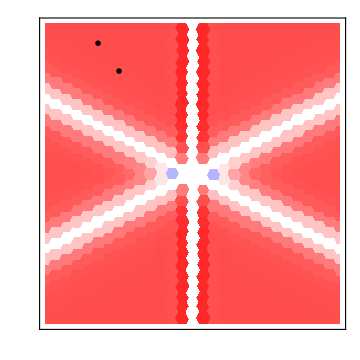

```mathematica
Grid[scPlots]
```

```mathematica
SavePlots[]:=(
Do[(
Do[(
Do[(
fileName=StringJoin["plots/",head,"/",
head,"_L=",ToString[scAvail["size"][[iN]]],
"_J=",ToString[scAvail["coupling"][[iJ]]],
"_B=",ToString[scAvail["interaction"][[iB]]],
".jpg"];
Export[fileName,scPlots[[iN,iJ,iB]],ImageResolution->300];
),{iB,Length[scAvail["interaction"]//Normal]}]
),{iJ,Length[scAvail["coupling"]//Normal]}]
),{iN,Length[scAvail["size"]//Normal]}]
)
```

```mathematica
SavePlots[]
```